Green Armor BFR vol% Histograms (E, F, G1 and G2)

```mathematica
filenameVolumeBase="G1_";
concFRG1=Import[pathVolumesFitted<>filenameVolumeBase<>"vol_percent_Unburntcropped_MF1_FR.h5",{"Datasets","concFR"}];
Dimensions[concFRG1]
```

{200,112,251}

```mathematica
SeedRandom[1]; 
listOfNonZeroVoxels = Select[Flatten[concFRG1],#>0&];//Timing
Length[listOfNonZeroVoxels]
concFRG1 = RandomSample[listOfNonZeroVoxels,numberOfVoxels];
Length[concFRG1]
```

{5.30719,Null}

5622375

1000000

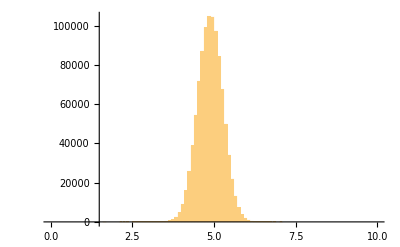

4.88396

0.374918

```mathematica
Histogram[concFRG1,{0.0,10,0.1}]
Mean[concFRG1]
StandardDeviation[concFRG1]
```

```mathematica
filenameVolumeBase="G1_";
concFRG1=Import[pathVolumesFitted<>filenameVolumeBase<>"vol_percent_MF1_FR.h5",{"Datasets","concFR"}];
Dimensions[concFRG1]
```

{200,510,324}

```mathematica
SeedRandom[1]; 
listOfNonZeroVoxels = Select[Flatten[concFRG1],#>0&];//Timing
Length[listOfNonZeroVoxels]
concFRG1 = RandomSample[100*listOfNonZeroVoxels,numberOfVoxels];
Length[concFRG1]
```

{2.18767,Null}

1000000

1000000

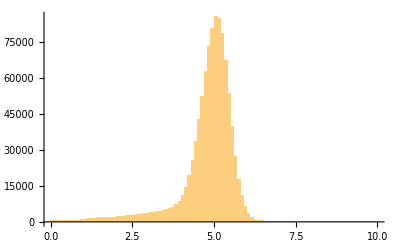

4.80127

0.854619

```mathematica
Histogram[concFRG1,{0.0,10,0.1}]
Mean[concFRG1]
StandardDeviation[concFRG1]
```

Sb2O3 plots Green Armor

```mathematica
filenameVolumeBase="G1_";
concSb2O3G1=Import[pathVolumesFitted<>filenameVolumeBase<>"vol_percent_Unburntcropped_MF1_Sb2O3.h5",{"Datasets","concSb2O3"}];
Dimensions[concSb2O3G1]
```

Import::nffil: File not found during Import.

{}

```mathematica
SeedRandom[1]; 
listOfNonZeroVoxels = Select[Flatten[concSb2O3G1],#>0&];//Timing
Length[listOfNonZeroVoxels]
concSb2O3G1 = RandomSample[listOfNonZeroVoxels,numberOfVoxels];
Length[concSb2O3G1]
```

{4.99324,Null}

6652858

1000000

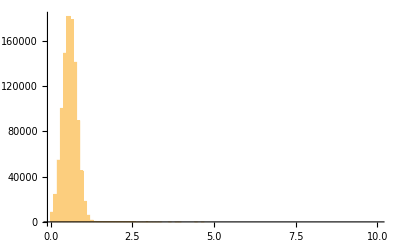

0.589962

0.212589

4.62866

```mathematica
Histogram[concSb2O3G1,{0.0,10,0.1}]
Mean[concSb2O3G1]
StandardDeviation[concSb2O3G1]
Max[concSb2O3G1]
```

```mathematica
.........................................................................
```

```mathematica
filenameVolumeBase="A1_";
pathVolumesFitted="/melete-nas01/lsu/scratch/olatinwo/CAMD_Nov2012/Cropped_New_Nov2012_K-edge/"
concSb2O3A1=Import[pathVolumesFitted<>filenameVolumeBase<>"vol_percent2_MF1_Sb2O3.h5",{"Datasets","concSb2O3"}];
Dimensions[concSb2O3A1]
```

/melete-nas01/lsu/scratch/olatinwo/CAMD_Nov2012/Cropped_New_Nov2012_K-edge/

{300,500,324}

```mathematica
filenameVolumeBase="F1_";
concSb2O3F1=Import[pathVolumesFitted<>filenameVolumeBase<>"vol_percent3_MF1_Sb2O3.h5",{"Datasets","concSb2O3"}];
Dimensions[concSb2O3F1]
```

{312,874,820}

```mathematica
filenameVolumeBase="G1_";
concSb2O3G1=Import[pathVolumesFitted<>filenameVolumeBase<>"vol_percent_MF1_Sb2O3.h5",{"Datasets","concSb2O3"}];
Dimensions[concSb2O3G1]
```

{200,510,324}

```mathematica
filenameVolumeBase="G2_";
concSb2O3G2=Import[pathVolumesFitted<>filenameVolumeBase<>"vol_percent_MF1_Sb2O3.h5",{"Datasets","concSb2O3"}];
Dimensions[concSb2O3G2]
```

{200,730,500}

```mathematica
SeedRandom[1]; numberOfVoxels=1000000;
listOfNonZeroVoxels = Select[Flatten[concSb2O3A1],#>0&];//Timing
Length[listOfNonZeroVoxels]
concSb2O3A1 = RandomSample[100*listOfNonZeroVoxels,numberOfVoxels];
Length[concSb2O3A1]

SeedRandom[1];
listOfNonZeroVoxels = Select[Flatten[concSb2O3F1],#>0&];//Timing
Length[listOfNonZeroVoxels]
concSb2O3F1 = RandomSample[100*listOfNonZeroVoxels,numberOfVoxels];
Length[concSb2O3F1]

SeedRandom[1]; 
listOfNonZeroVoxels = Select[Flatten[concSb2O3G1],#>0&];//Timing
Length[listOfNonZeroVoxels]
concSb2O3G1 = RandomSample[100*listOfNonZeroVoxels,numberOfVoxels];
Length[concSb2O3G1]

SeedRandom[1]; 
listOfNonZeroVoxels = Select[Flatten[concSb2O3G2],#>0&];//Timing
Length[listOfNonZeroVoxels]
concSb2O3G2 = RandomSample[100*listOfNonZeroVoxels,numberOfVoxels];
Length[concSb2O3G2]
```

{30.2414,Null}

47393547

1000000

{230.848,Null}

109356506

1000000

{22.3096,Null}

27465032

1000000

{41.0838,Null}

45860465

1000000

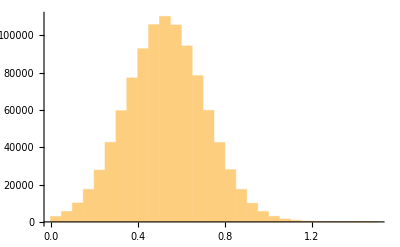

0.528487

0.190001

```mathematica
Histogram[concSb2O3A1,{0.0,1.5,0.05}]
Mean[concSb2O3A1]
StandardDeviation[concSb2O3A1]
```

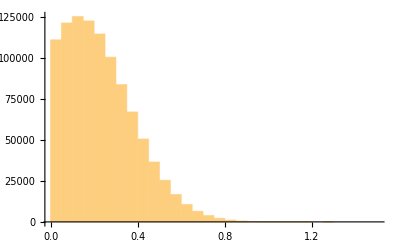

0.233412

0.159414

```mathematica
Histogram[concSb2O3F1,{0.0,1.5,0.05}]
Mean[concSb2O3F1]
StandardDeviation[concSb2O3F1]
```

```mathematica
list =HistogramList[concSb2O3A1,{0.0,100,0.05}];
threshold=0.8;  (* based on A1 *)
indexThreshold=Position[list[[1]],p_?(#==threshold&)][[1,1]]
volPercentNumerator = Table[Mean[{list[[1,i]],list[[1,i+1]]}]*list[[2,i]], {i,indexThreshold,Length[list[[1]]]-1}];
volPercentDenominator = Table[Mean[{list[[1,i]],list[[1,i+1]]}]*list[[2,i]], {i,1,Length[list[[1]]]-1}];
volPercentNumerator = Total[volPercentNumerator]
volPercentDenominator = Total[volPercentDenominator]
fractionSb2O3inlumps = 100*volPercentNumerator/volPercentDenominator
```

17

61160.9

528463.

11.5734

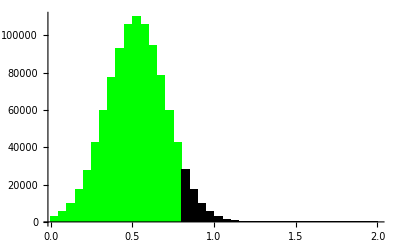

```mathematica
listBelowThreshold = Histogram[Select[concSb2O3A1,#<threshold &],{0,2,0.05},ChartStyle->Directive[Green,EdgeForm[]]];
listAboveThreshold = Histogram[Select[concSb2O3A1,#>=threshold &],{0,2,0.05},ChartStyle->Directive[Black,EdgeForm[]]];
gSb2O3A1=Show[{listBelowThreshold,listAboveThreshold}]
```

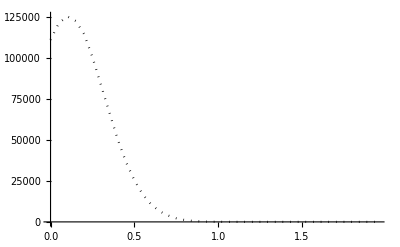
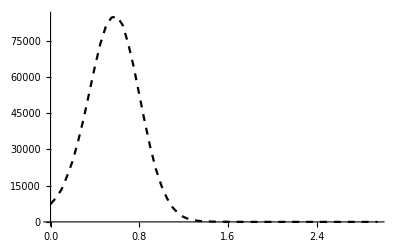
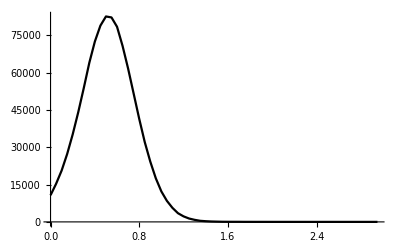

```mathematica
data =HistogramList[concSb2O3F1,{0,2,0.05}];
gSb2O3F1 = ListLinePlot[Transpose[{Drop[data[[1]],-1],data[[2]]}],PlotRange->All,PlotStyle->Directive[Black,Dotted]];
data =HistogramList[concSb2O3G1,{0,3,0.05}];
gSb2O3G1 = ListLinePlot[Transpose[{Drop[data[[1]],-1],data[[2]]}],PlotRange->All,PlotStyle->Directive[Black,Dashed]];
data =HistogramList[concSb2O3G2,{0,3,0.05}];
gSb2O3G2 = ListLinePlot[Transpose[{Drop[data[[1]],-1],data[[2]]}],PlotRange->All,PlotStyle->Directive[Black]];
{gSb2O3F1,gSb2O3G1,gSb2O3G2}
```

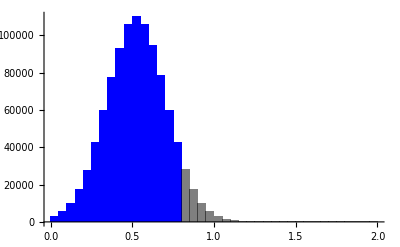

```mathematica
gHistA1=Histogram[{
Select[concSb2O3A1,#<threshold &],
Select[concSb2O3A1,#>=threshold &]},{0,2,0.05},
ChartStyle->{ Directive[Blue,Opacity[1],EdgeForm[]],Directive[Black,EdgeForm[]]}]
```

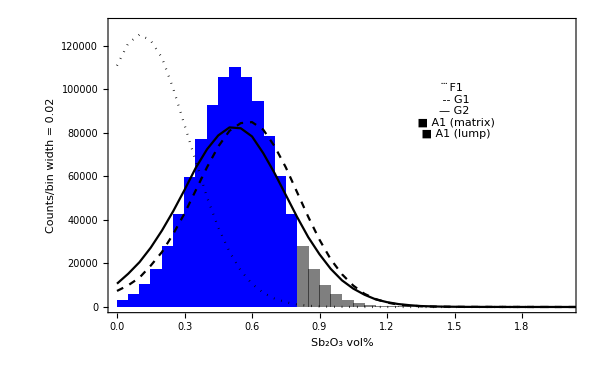

```mathematica
Show[{gHistA1,gSb2O3F1,gSb2O3G1,gSb2O3G2},PlotRange->{{0,2.0},{0,130000}},
Frame->True,FrameStyle->14,ImageSize->600,
FrameLabel->{{"Counts/bin width = 0.02",""},{"Sb_2O_3 vol%",""}},
Epilog->Style[Text[Framed[" ⃛ F1\n -- G1\n— G2\n ■ A1 (matrix)\n ■ A1 (lump)"],{1.5,90000}],16,TextAlignment->Right]]
```

```mathematica
TableForm[
{{"A1", Mean[concSb2O3A1],StandardDeviation[concSb2O3A1],Max[concSb2O3A1]},
{"G1", Mean[concSb2O3G1],StandardDeviation[concSb2O3G1],Max[concSb2O3G1]},
{"G2", Mean[concSb2O3G2],StandardDeviation[concSb2O3G2],Max[concSb2O3G2]},
{"F1", Mean[concSb2O3F1],StandardDeviation[concSb2O3F1],Max[concSb2O3F1]}}, 
TableHeadings->{None,{"sample","average","standard deviation", "maximum"}}]

TableForm[
{{"A1", threshold,fractionSb2O3inlumps}}, 
TableHeadings->{None,{"sample","threshold","fraction in lumps"}}]
```

sample | average | standard deviation | maximum
A1 | 0.528487 | 0.190001 | 12.2651
G1 | 0.593219 | 0.233796 | 5.22248
G2 | 0.552281 | 0.251919 | 17.383
F1 | 0.233412 | 0.159414 | 1.87507

sample | threshold | fraction in lumps
A1 | 0.8 | 11.5734